4)Используя таблицу значений функции f(x) в равноотстоящих точках
отрезка [0, 6], полученной в задании 1 при n = 10, выполнить следующие действия:
а) построить интерполяционный кубический сплайн дефекта 1 S_3(x) для функции f(x), проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и S_3(x) на одном чертеже);
б) выполнить интерполяцию сплайном Sf(x) с помощью функции
Interpolation[data, Method->"Spline"], проиллюстрировать графически;
в) построить интерполяционный кубический сплайн Spl с помощью
функции SplineFit[data, Cubic] (предварительно загрузить пакет сплайн-интерполяции командой Needs["Splines`"]), проиллюстрировать графически (для построения графика сплайна Spl использовать функцию ParametricPlot);
г) вычислить значения функции f(x) и построенных интерполяционных
сплайнов S_3(x), Sf(x) иSpl в точке x = 2,4316.
Функция f(x):

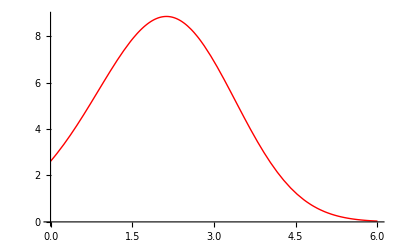

```mathematica
f[x_]= (x + √(π+1))* Exp[-4/39*√(x^5)+5*x/9+1/4];
a=0;b=6;n=10;x0=2.4316;h=(b-a)/n;
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
(*Возьмём таблицу значений функции для равноотстоящих узлов(Subscript[h, i] =h) на промежутке для n=10:*)
data=Table[{a+i* h,f[a+i* h]},{i,0,n}]//N;
TableForm[data]
```

0. | 2.61311
0.6 | 4.58895
1.2 | 6.88217
1.8 | 8.57075
2.4 | 8.65092
3. | 6.91907
3.6 | 4.29295
4.2 | 2.02528
4.8 | 0.712835
5.4 | 0.183836
6. | 0.0341457

```mathematica
(*Для получения кубического сплайна дефекта 1 найдём коэффициенты Subscript[c, k] с помощью встроенной функцииLinearSolve*)
listC=Table[0,{i,0,n}];
A=Table[0,{n-1},{n-1}];
Do[If[i≠1,A[[i,i-1]]=h];A[[i,i]]=4 h;If[i≠n-1,A[[i,i+1]]=h],{i,1,n-1}]
A//MatrixForm//N
```

(2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4)

```mathematica
(*Столбец свободных членов:*)
B=Table[3 ((data[[i,2]]-data[[i-1,2]])/h-(data[[i-1,2]]-data[[i-2,2]])/h),{i,3,n+1}]//N;
X=LinearSolve[A,B];
For[i=1,i≤n-1,i++,listC[[i+1]]=X[[i]]];
MatrixForm[listC]
```

(0
0.879696
-0.873858
-2.42303
-2.83743
-1.32735
0.69452
1.5363
1.12058
0.510078
0)

```mathematica
(*Зададим остальные коэффициенты кубического сплайна:*)
listA=Table[data[[i+1,2]],{i,1,n}]
```

{4.58895,6.88217,8.57075,8.65092,6.91907,4.29295,2.02528,0.712835,0.183836,0.0341457}

```mathematica
listB=Table[(data[[i,2]]-data[[i-1,2]])/h+2/3 h listC[[i]]+1/3 h listC[[i-1]],{i,2,n+1}]
```

{3.64494,3.64844,1.67031,-1.48597,-3.98483,-4.36453,-3.02604,-1.43191,-0.453516,-0.147469}

```mathematica
listD=Table[(listC[[i]]-listC[[i-1]])/(3 h),{i,2,n+1}]
```

{0.48872,-0.974197,-0.860651,-0.230222,0.838936,1.12326,0.467653,-0.230951,-0.339169,-0.283377}

```mathematica
(*Теперь зададим кубический сплайн в виде кусочно заданной функции:*)
sData=Table[{listA[[i]]+listB[[i]] (x-data[[i+1,1]])+listC[[i+1]] ((x-data[[i+1,1]])^2)+listD[[i]] ((x-data[[i+1,1]])^3),data[[i,1]]≤x≤data[[i+1,1]]}, {i,1,n}]//Simplify
S[x_]=Piecewise[sData]
```

Piecewise[{{2.61311+3.11712 x+0.48872 x^3, 0.≤x≤0.6}, {2.9291+1.53717 x+2.63325 x^2-0.974197 x^3, 0.6≤x≤1.2}, {2.73289+2.02769 x+2.22449 x^2-0.860651 x^3, 1.2≤x≤1.8}, {-0.943773+8.15546 x-1.17983 x^2-0.230222 x^3, 1.8≤x≤2.4}, {-15.7238+26.6305 x-8.87777 x^2+0.838936 x^3, 2.4≤x≤3.}, {-23.4005+34.3072 x-11.4367 x^2+1.12326 x^3, 3.≤x≤3.6}, {7.18742+8.81728 x-4.35613 x^2+0.467653 x^3, 3.6≤x≤4.2}, {58.9456-28.1529 x+4.44628 x^2-0.230951 x^3, 4.2≤x≤4.8}, {70.9136-35.6329 x+6.00462 x^2-0.339169 x^3, 4.8≤x≤5.4}, {62.1284-30.7522 x+5.10078 x^2-0.283377 x^3, 5.4≤x≤6.}, {0, True}}]

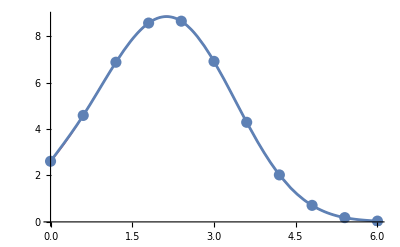

```mathematica
(*Изобразим полученный кубический сплайн.*)
graphD=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
graphS=Plot[S[x],{x,a,b}];
Show[graph,graphD,graphS]
```

б) Интерполируем функцию сплайном с помощью функции Interpolation :

```mathematica
Sf[x_]=Interpolation[data,x,Method->"Spline"]
```

InterpolatingFunction[…][x]

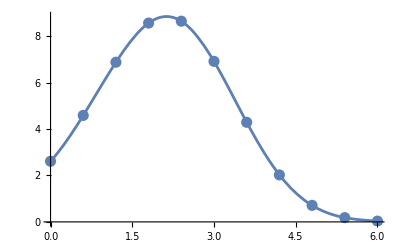

```mathematica
(*Изобразим полученный сплайн.*)
graphSf=Plot[Sf[x],{x,a,b}];
Show[graph,graphD,graphSf]
```

в) Получим интерполяционный кубический сплайн с помощью функции SplineFit :

```mathematica
Needs["Splines`"]
Spl=SplineFit[data,Cubic]
```

SplineFunction[Cubic, {0.,10.}, <>]

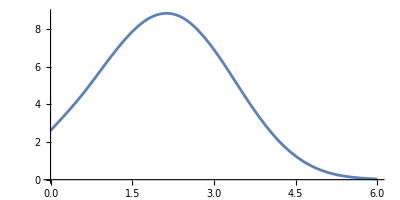

```mathematica
(*Изобразим полученный сплайн.*)
t=(x-a)/h;
graphSpl=ParametricPlot[Spl[t],{t,0,n},AspectRatio->1/2]
```

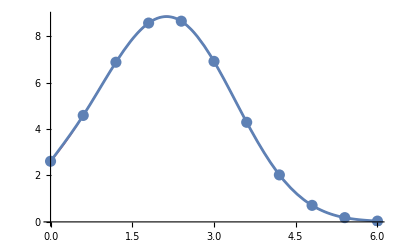

```mathematica
Show[graph,graphD,graphSpl]
```

г) Значение интерполяционного кубического сплайна в точке x0:

```mathematica
Print["f[x0]=",f[x0]]
```

f[x0]=8.60116

```mathematica
Print["S[x0]=",S[x0]]
```

S[x0]=8.60116

```mathematica
(*Значение интерполирующей функции-сплайна в точке x0:*)
```

```mathematica
Print["Sf[x0]=",Sf[x0]]
```

Sf[x0]=8.60107

```mathematica
(*Значение интерполяционного кубического сплайна,построенного с помощьюSplineFit,в точке x0:*)
Print["Spl[x0]=",Last[Spl[(x0-a)/h]]]
```

Spl[x0]=8.60116